Symbolic integration of the cosine-weighted constant visibility function ∫cosθ sinθⅆθ= -1/2 cos^2 θ
Integration over the entire hemisphere ∫_0^(2π) ∫_0^(π/2) cosθ sinθⅆθⅆϕ=π

```mathematica
2π * Integrate[Cos[θ]Sin[θ],{θ,0,π/2}]
```

π

We can then assume that the Ambient Occlusion value of a flat, unoccluded surface should equal π, which is then scaled to 1 to be stored into a classical AO texture.
So let’s decide that an AO map’s value should be scaled by π when read by a shader, multiplied by ρ/πthe surface’s albedo to obtain a [0,1] ambient reflectance value, then multiplied by the irradiance perceived by the surface to finally obtain the reflected radiance in the outgoing direction ω_o:
	L(x,ω_o) = ρ/π (π AO)E(x)=ρ AO E(x)

We can write the “direct” irradiance estimate as:
	E_0(x)=∫_Ω^□ L_0 V_dir(ω_i)(n.ω_i)ⅆ ω_i
Where L_0=1 and V_dir(ω_i) represents the direct visibility function that equals 1 if the ray is unoccluded by the surface, 0 otherwise.
We notice that E_0(x) is exactly the value computed for the Ambient Occlusion, so E_0(x)=AO.

We can then write the general expression for the “indirect” irradiance estimate as:
	E_(n+1)(x)=∫_Ω^□ L_i(x,ω_i )V_ind(ω_i)(n.ω_i)ⅆ ω_i
Where V_ind(ω_i) represents the indirect visibility function that equals 1 if the ray is occluded by the surface, 0 otherwise (so V_ind(ω_i)=1-V_dir(ω_i) ).
We can rewrite the perceived incoming luminance L_i(x,ω_i ) from a neighbor location x' as:
	L_i(x,ω_i )=ρ/π E_n(x')
And finally:
	E_(n+1)(x)=∫_Ω^□ ρ/π E_n(x')V_ind(ω_i)(n.ω_i)ⅆ ω_i

We easily see that we can compute the irradiance incrementally by re-using the previous irradiance at the indirect neighbor locations.

## Fitting Experimental Data

After writing the program that computes the AO and the multiple indirect bounces from a height map, we collect the bounced illuminance values into histograms where the bin indices are given by the AO values: this bascially computes the average indirect illuminance perceived by a point given its AO value (AO value is in [0,π] but we rescaled it to [0,1] for convenience).
We do that for multiple bounces to try and find a pattern in the shape and amplitude of the curves...

To generate the curves shown below, we used the WallHeight.png as a height map, and its corresponding WallNormal.png as a normal map.
We also chose a height value of 5 cm for a total wall length of 1 meter, 1024 rays at 179° cone aperture.
It gave some nice curves without the annoying artefacts found at the extremas that can be found with other maps.

```mathematica
ClearAll["Global`*"]
```

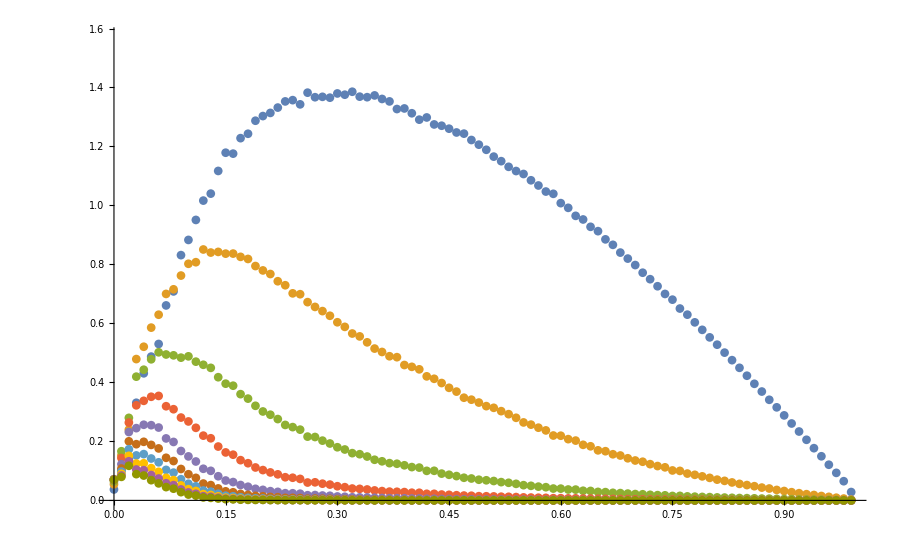

```mathematica
SetDirectory[NotebookDirectory[]]; 
tableSize = 100;
bouncesCount = 10;
rawArray=Table[ BinaryReadList["WallHeight"<>ToString[i]<>".float", "Real32"],{i,1,bouncesCount}];
bounces = Table[Table[{(i-1)/tableSize,rawArray[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];
ListPlot[bounces,PlotRange->{0,π/2}]
```

Intuitively, it looks like a log-normal distribution curve that we can model as f(x)=a*x*(1-x)*e^-bx.
We can see below that it’s actually a very nice fit for the curves and may even deduce a general rule to find a and b coefficients as a function of the bounce index...

```mathematica
Manipulate[Plot[8*x*(1-x)*ⅇ^(-k*x),{x,0,1},PlotRange->{0,π/2}],{{k,1},0,20}]
```

```mathematica
Clear[a,b]
model=b/a*x*(1-x)*Exp[-b*x];
fitter[i_]:=Module[{},
FindFit[bounces[[i]], model,{a,{b,20}},{x}]
]
fits=Table[fitter[bounceIndex],{bounceIndex,1,bouncesCount}]
```

{{a→0.145266,b→1.55043},{a→0.360125,b→4.9367},{a→0.662865,b→9.62783},{a→1.00588,b→16.3854},{a→1.36116,b→22.712},{a→1.74407,b→27.4423},{a→2.15167,b→31.166},{a→2.57505,b→34.4689},{a→3.00497,b→37.6836},{a→3.43309,b→40.9832}}

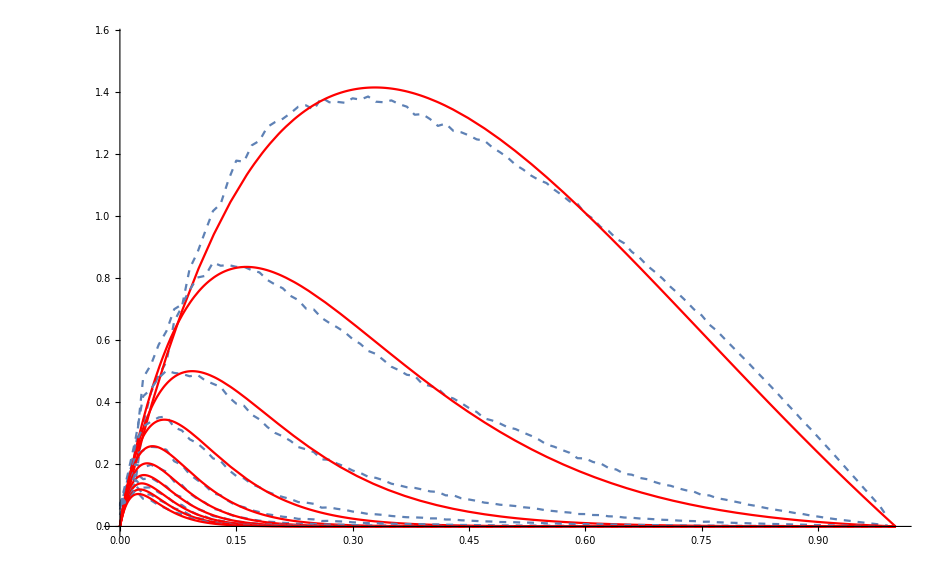

```mathematica
Show[
Table[{ListLinePlot[bounces[[bounceIndex]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[model/.fits[[bounceIndex]],{x,0,1},PlotRange->Full,PlotStyle->Red]},{bounceIndex,1,bouncesCount}]
]
```

Now we plot the various a and b coefficients as a function of the bounce index:

{0.145266,0.360125,0.662865,1.00588,1.36116,1.74407,2.15167,2.57505,3.00497,3.43309}

{1.55043,4.9367,9.62783,16.3854,22.712,27.4423,31.166,34.4689,37.6836,40.9832}

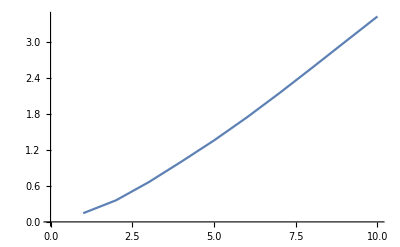

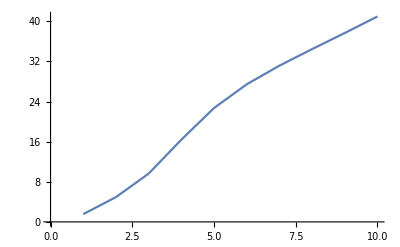

```mathematica
coeffsA=Table[a/.fits[[bounceIndex]],{bounceIndex,1,bouncesCount}]
coeffsB=Table[b/.fits[[bounceIndex]],{bounceIndex,1,bouncesCount}]
ListLinePlot[coeffsA,PlotRange->Full]
ListLinePlot[coeffsB,PlotRange->Full]
```

We notice the curves are almost linear so let’s try and fit the a and b coefficients as a linear function of the bounce index:

{a0→0.,a1→0.251994,a2→0.0130302}

FindFit::fmgz: Encountered a gradient that is effectively zero. The result returned may not be a minimum; it may be a maximum or a saddle point.

{b0→1.,b1→1.,b2→1.,b3→1.}

Function[{x},1.55043+3.93698 (-1+x)]

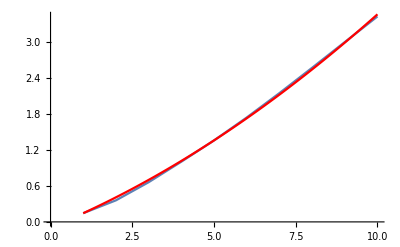

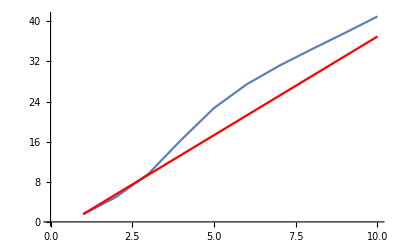

```mathematica
modelA=coeffsA[[1]]+0*a0+a1*(x-1)+a2*(x-1)^2;
modelB=coeffsB[[1]]+0*b0+b1*(x-1)+b2*(x-1)^2+b3*(x-1)^3;
modelB=coeffsB[[1]]+0*b0+b1*(x-1);
modelB=coeffsB[[1]]+(x-1)/(bouncesCount-1)*(coeffsB[[bouncesCount]] - coeffsB[[1]] - 4);
modelFitA=FindFit[coeffsA,modelA,{a0,a1,a2},{x}]
modelFitB=FindFit[coeffsB,modelB,{b0,b1,b2,b3},{x}]
(*Show[ListPlot[coeffsA,PlotRange->Full],Plot[modelA/.modelFitA,{x,0,bouncesCount}]]
Show[ListPlot[coeffsB,PlotRange->Full],Plot[modelB/.modelFitB,{x,0,bouncesCount}]]*)

modelFitA=Function[{x},Evaluate[modelA/.modelFitA]];
modelFitB=Function[{x},Evaluate[modelB/.modelFitB]]
Show[ListLinePlot[coeffsA,PlotRange->Full],Plot[modelFitA[x],{x,1,bouncesCount},PlotStyle->Red]]
Show[ListLinePlot[coeffsB,PlotRange->Full],Plot[modelFitB[x],{x,1,bouncesCount},PlotStyle->Red]]
```

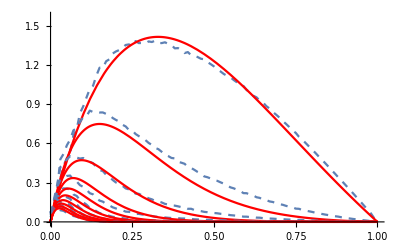

```mathematica
Show[
Table[{ListLinePlot[bounces[[bounceIndex]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[model/.{a-> modelFitA[bounceIndex],b-> modelFitB[bounceIndex]},{x,0,1},PlotRange->Full,PlotStyle->Red]},{bounceIndex,1,bouncesCount}]
]
```

{10.673,13.7083,14.5246,16.2896,16.6857,15.7346,14.4846,13.3858,12.5404,11.9377}

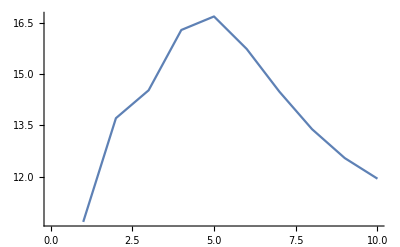

```mathematica
finalCoeffs=Table[coeffsB[[i]]/coeffsA[[i]],{i,1,bouncesCount}]
ListLinePlot[finalCoeffs]
```

## Refitting with Constrained b

Assuming b=?? we can try and re-fit the remaining variable a:

```mathematica
Clear[a,b]
fitter[i_]:=Module[{},
b = modelFitB[i];
FindFit[bounces[[i]], model,{a},{x}]
];
fits=Table[fitter[bounceIndex],{bounceIndex,1,bouncesCount}];
newCoeffsA=Table[a/.fits[[bounceIndex]],{bounceIndex,1,bouncesCount}]
Clear[a,b]
```

{0.145266,0.354521,0.667576,1.10147,1.56096,1.99283,2.40315,2.80657,3.20964,3.6127}

0.145266+0.385271 (-1+x)

0.145266+a0 (-1+x)+a1 (-1+x)^2

0.145266+a0 (-1+x)+a1 (-1+x)^2+a2 (-1+x)^3

{a0→0.19848,a1→0.048556,a2→-0.00312863}

a0→0.19848

a1→0.024278

{a0→0.19848,a1→0.024278,a2→0.}

Function[{x},0.145266+0.19848 (-1+x)+0.024278 (-1+x)^2]

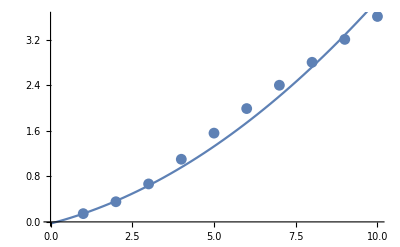

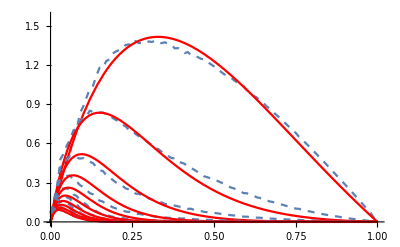

```mathematica
Clear[a0,a1,a2]
modelA=newCoeffsA[[1]]+(x-1)/(bouncesCount-1)*(newCoeffsA[[bouncesCount]]-newCoeffsA[[1]])
modelA=newCoeffsA[[1]]+a0*(x-1)+a1*(x-1)^2
modelA=newCoeffsA[[1]]+a0*(x-1)+a1*(x-1)^2+a2*(x-1)^3
modelFitA=FindFit[newCoeffsA,modelA,{a0,a1,a2},{x}]
modelFitA[[1]]=a0-> 1.0*(a0/.modelFitA[[1]])
modelFitA[[2]]=a1-> 0.5*(a1/.modelFitA[[2]])
modelFitA[[3]]=a2-> 0.0;
modelFitA
modelFitA=Function[{x},Evaluate[modelA/.modelFitA]]
Show[ListPlot[newCoeffsA,PlotRange->Full],Plot[modelFitA[x],{x,0,bouncesCount}]]
Clear[a,b]
Show[
Table[{ListLinePlot[bounces[[bounceIndex]],PlotRange->{{0,1},{0,π/2}},PlotStyle->Dashed],
Plot[model/.{ b-> modelFitB[bounceIndex],a->modelFitA[bounceIndex]},{x,0,1},PlotRange->Full,PlotStyle->Red]},{bounceIndex,1,bouncesCount}]
]
```

Reference graph without manual change of fitting variables (a0,a1,a2):

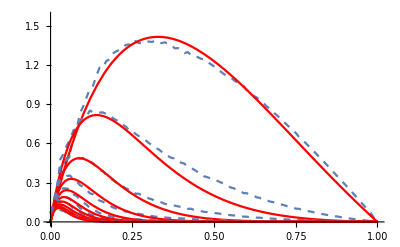

## Using Fitted Data

Okay so we ended up with these expressions for a and b coefficients depending on i, the bounce index:
	a=0.145266+0.19848 (i-1)+0.024278 (i-1)^2
	b=1.55043+3.93698 (i-1)

We plug these into the reflectance model depending on α=AO/π:
	f(α,i)=b/a*α*(1-α)*ⅇ^(-b α)

As agreed, we assume the surface albedo ρ is constant in the surrounding of the luminance estimate and we can compute the final luminance due to indirect bounce on the surface as:

	L_indirect(x,ω_o) = 1/π[ρ AO(x) + ∑_(i=1)^N ρ^i f((AO(x))/π,i)]  E(x)

We notice the interesting property of albedo saturation as the amount of bounces increases.

## Verifying

We open the ρ = 0.5 curves

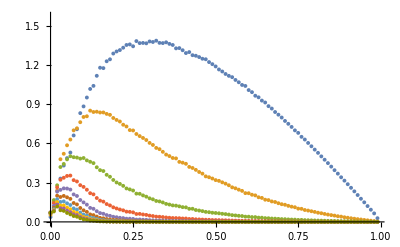

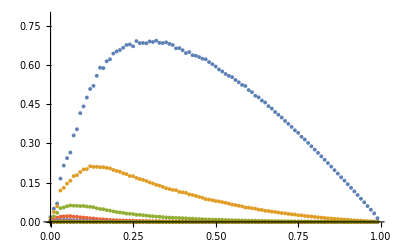

```mathematica
rawArray05=Table[ BinaryReadList["WallHeight"<>ToString[i]<>" - rho=0.5.float", "Real32"],{i,1,bouncesCount}];
bounces05 = Table[Table[{(i-1)/tableSize,rawArray05[[bounceIndex]][[i]]},{i,1,tableSize}],{bounceIndex,1,bouncesCount}];
ListPlot[bounces,PlotRange->{0,π/2}]
ListPlot[bounces05,PlotRange->{0,π/4}]
```

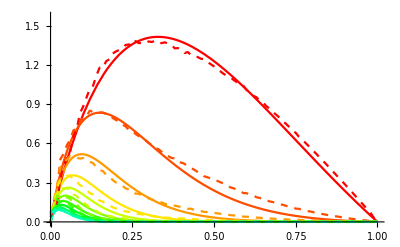

```mathematica
a[i_]:=0.14526642906187737+0.1984799936582921 (i-1)+0.024277999559107394 (i-1)^2
b[i_]:=1.5504282580946984+3.936979219376581 (i-1)
f[α_,i_]:=b[i]/a[i] α(1-α)ⅇ^(-b[i]α)
Show[Table[Plot[f[x,i],{x,0,1},PlotRange->{{0,1},{0,π/2}},PlotStyle->Hue[(i-1)/20]],{i,1,10}],
Table[ListLinePlot[bounces[[i]],PlotRange->Full,PlotStyle->{Dashed,Hue[(i-1)/20]}],{i,1,10}]]
```

And now for the moment of truth:

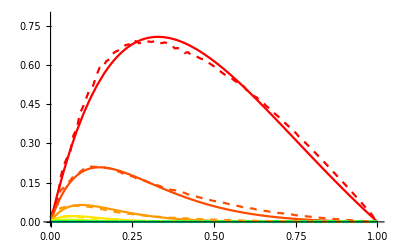

```mathematica
ρ=0.5;
Show[Table[Plot[ρ^i* f[x,i],{x,0,1},PlotRange->{{0,1},{0,π/4}},PlotStyle->Hue[(i-1)/20]],{i,1,10}],
Table[ListLinePlot[bounces05[[i]],PlotRange->Full,PlotStyle->{Dashed,Hue[(i-1)/20]}],{i,1,10}]]
```

{a→6.8839,b→1.55043}

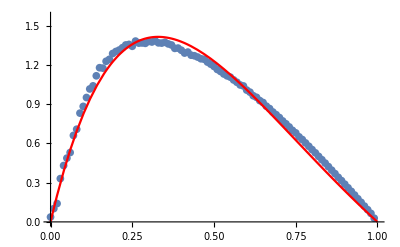

```mathematica
modelFit1=FindFit[bounces[[1]], model,{a,b},{x}]
bounce1=Function[{x},Evaluate[model/.modelFit1]];
Show[
ListPlot[bounces[[1]],PlotRange->{{0,1},{0,π/2}}],
Plot[bounce1[x],{x,0,1},PlotStyle->Red]
]
```

{a→2.77681,b→4.9367}

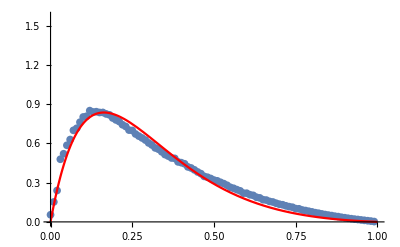

```mathematica
modelFit2=FindFit[bounces[[2]], model,{a,b},{x}]
bounce2=Function[{x},Evaluate[model/.modelFit2]];
Show[
ListPlot[bounces[[2]],PlotRange->{{0,1},{0,π/2}}],
Plot[bounce2[x],{x,0,1},PlotStyle->Red]
]
```

{a→1.5086,b→9.62783}

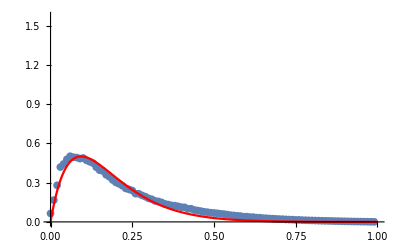

```mathematica
modelFit3=FindFit[bounces[[3]], model,{a,b},{x}]
bounce3=Function[{x},Evaluate[model/.modelFit3]];
Show[
ListPlot[bounces[[3]],PlotRange->{{0,1},{0,π/2}}],
Plot[bounce3[x],{x,0,1},PlotStyle->Red]
]
```

{a→0.994155,b→16.3854}

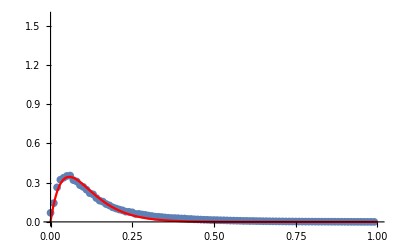

```mathematica
modelFit4=FindFit[bounces[[4]], model,{a,b},{x}]
bounce4=Function[{x},Evaluate[model/.modelFit4]];
Show[
ListPlot[bounces[[4]],PlotRange->{{0,1},{0,π/2}}],
Plot[bounce4[x],{x,0,1},PlotStyle->Red]
]
```

{6.8839,2.77681,1.5086,0.994155}

{1.55043,4.9367,9.62783,16.3854}

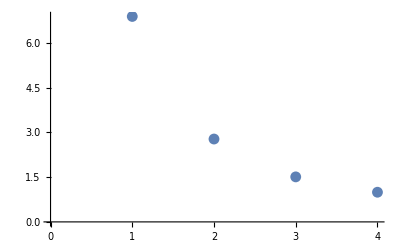

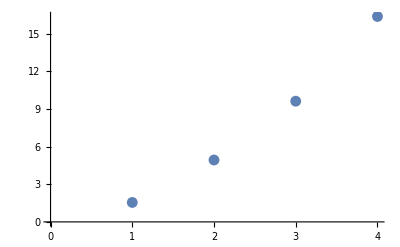

```mathematica
coeffsA={a/.modelFit1,a/.modelFit2,a/.modelFit3,a/.modelFit4}
coeffsB={b/.modelFit1,b/.modelFit2,b/.modelFit3,b/.modelFit4}
ListPlot[coeffsA]
ListPlot[coeffsB]
```